## Imaginary part of Heaviside

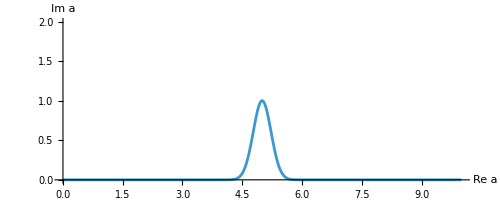

```mathematica
z0=5; (*position of source peak*)
J=1;  (*Gaussian height*)

(*Contour definition*)γ[a_]:=a+I J Exp[-10 (a-z0)^(2)];
γp[a_]:=D[γ[a],a];
γpp[a_]:=D[γ[a],{a,2}];

(*Plot in the complex plane,clipping the huge tails in Im[z]*)
ParametricPlot[{Re[γ[a]],Im[γ[a]]},{a,0,10},AxesLabel->{"Re a","Im a"},PlotRange->{All,{0,2}}]
```

### Compare integration of Dirac delta function to the extended analytical solution with the extended Heaviside (arbitrary boundary conditions)

```mathematica
SourceDelta=D[HeavisideTheta[r-r0]/.r0->5,r]
```

DiracDelta[-5+r]

```mathematica
ExtendedDiracDelta[r_,r0_]:=ⅈ/(π (r-r0))
```

```mathematica
HLog[r_,r0_]:=1+ I/Pi Log[r-r0]
```

```mathematica
Source=D[HLog[r,5],r]
```

ⅈ/(π (-5+r))

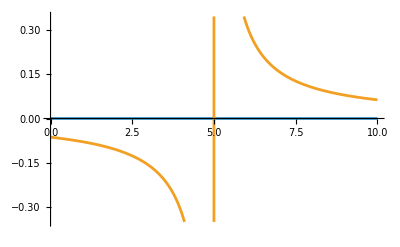

```mathematica
Plot[{Re[Source]/.r->a,Im[Source]/.r->a},{a,0,10}]
```

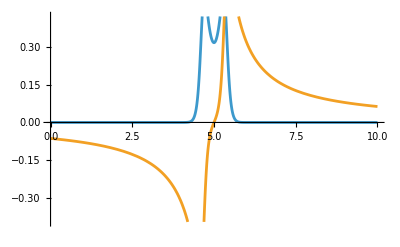

```mathematica
Plot[{Re[Source]/.r->γ[a],Im[Source]/.r->γ[a]},{a,0,10}]
```

```mathematica
ODE=Function[{r,l,S},D[ψ[r],{r,2}]+2/r D[ψ[r],{r,1}]-l(l+1)/r^2 ψ[r]==S]
```

Function[{r,l,S},∂_{r,2} ψ[r]+(2 ∂_{r,1} ψ[r])/r-(l (l+1) ψ[r])/r^2==S]

```mathematica
ODEHomo=ODE[r,0,SourceDelta]
```

(2 ψ'[r])/r+ψ''[r]==DiracDelta[-5+r]

```mathematica
BoundaryConditions={1,0}
```

{1,0}

```mathematica
(*Numerical solution (no Method specified)*)
solNumeric=NDSolveValue[{ODEHomo,ψ[1]==BoundaryConditions[[1]],ψ'[1]==BoundaryConditions[[2]]},ψ,{r,1,100},WorkingPrecision->50]
```

InterpolatingFunction[…]

```mathematica
r0
```

r0

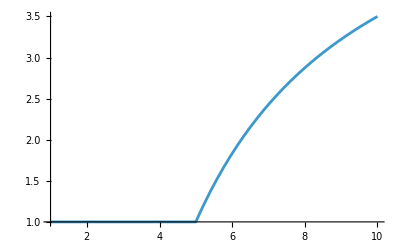

```mathematica
Plot[Re@solNumeric[r],{r,1,10}]
```

```mathematica
solAnalytic=DSolveValue[{ODE[r,0,SourceDelta],ψ[1]==BoundaryConditions[[1]],ψ'[1]==BoundaryConditions[[2]]},ψ,r]//Simplify
```

Function[{r},(r-25 HeavisideTheta[-5+r]+5 r HeavisideTheta[-5+r])/r]

```mathematica
solAnalyticExtended=solAnalytic/.HeavisideTheta[-5+r]->HLog[r,5]
```

Function[{r},(r-25 (1+(ⅈ Log[-5+r])/π)+5 r (1+(ⅈ Log[-5+r])/π))/r]

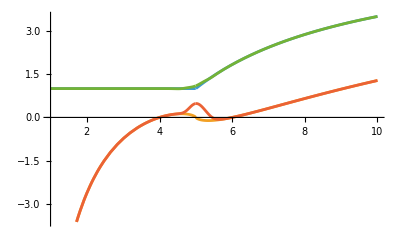

```mathematica
Plot[{Re@solAnalyticExtended[r],Im@solAnalyticExtended[r],Re@solAnalyticExtended[γ[r]],Im@solAnalyticExtended[γ[r]]},{r,1,10}]
```

```mathematica
ContourODEHomo3=Function[{a,l},Y''[a]+(-γpp[a]/γp[a]+2γp[a]/γ[a]) Y'[a]-l(l+1)γp[a]^2/γ[a]^2Y[a]==γp[a]^2 * (Source/.r->γ[a])]
```

Function[{a,l},Y''[a]+(-γpp[a]/γp[a]+(2 γp[a])/γ[a]) Y'[a]-(l (l+1) γp[a]^2 Y[a])/γ[a]^2==γp[a]^2 (Source/.r→γ[a])]

```mathematica
ContourODEHomo03=ContourODEHomo3[a,0]
```

((2 (1-20 ⅈ (-5+a) ⅇ^(-10 (-5+a)^2)))/(a+ⅈ ⅇ^(-10 (-5+a)^2))-(ⅈ (-20 ⅇ^(-10 (-5+a)^2)+400 (-5+a)^2 ⅇ^(-10 (-5+a)^2)))/(1-20 ⅈ (-5+a) ⅇ^(-10 (-5+a)^2))) Y'[a]+Y''[a]==(ⅈ (1-20 ⅈ (-5+a) ⅇ^(-10 (-5+a)^2))^2)/((-5+a+ⅈ ⅇ^(-10 (-5+a)^2)) π)

```mathematica
(* solAnalyticCont=DSolveValue[{ContourODEHomo[a,0],Y[1]==BoundaryConditions[[1]],Y'[1]==BoundaryConditions[[2]]},Y,a] *)
```

```mathematica
(*Solve along the contour:Y(a)=ψ(γ(a)) numerically *)
solNumericCont3=NDSolveValue[{ContourODEHomo3[a,0],Y[1]==BoundaryConditions[[1]],Y'[1]==BoundaryConditions[[2]]},Y,{a,1,100},WorkingPrecision->50]
```

InterpolatingFunction[{{1.0000000000000000000000000000000000000000000000000, 100.00000000000000000000000000000000000000000000000}}, <>]

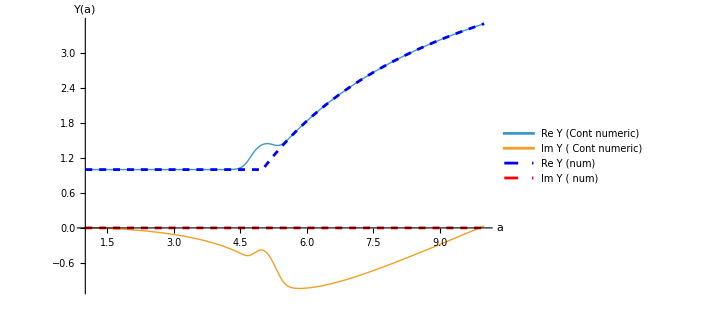

```mathematica
Plot[{Re[solNumericCont3[a]],Im[solNumericCont3[a]],Re[solNumeric[a]],Im[solNumeric[a]]},{a,1,10},PlotLegends->{"Re Y (Cont numeric)","Im Y ( Cont numeric)","Re Y (num)","Im Y ( num)"},AxesLabel->{"a","Y(a)"},PlotRange->All,ImageSize->520,PlotStyle->{{Thick},{Thick},{Dashed,Blue},{Dashed,Red}   }]
```

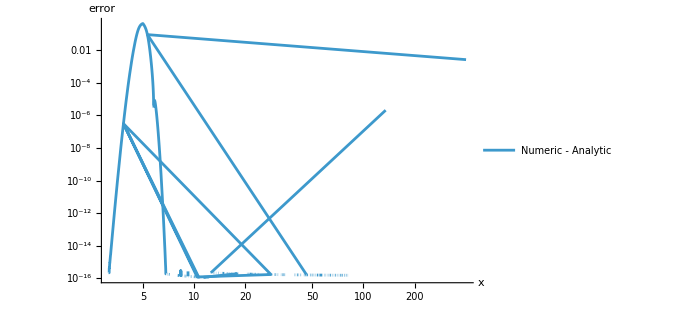

```mathematica
LogLogPlot[Abs[(Re@solNumericCont3[x]-(Re@solNumeric[x]))/(Re@solNumeric[x])],{x,1,100},PlotLegends->{"Numeric - Analytic"},AxesLabel->{"x","error"},PlotRange->All,ImageSize->500]
```

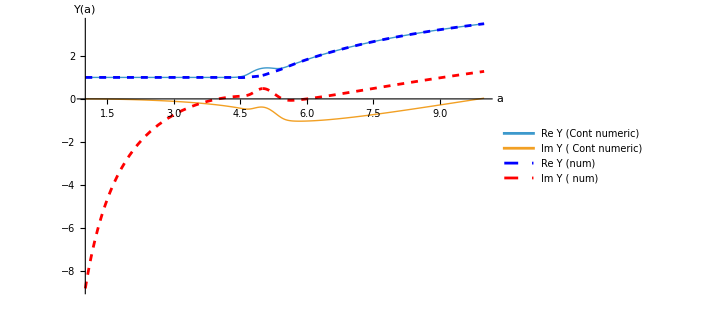

```mathematica
Plot[{Re[solNumericCont3[a]],Im[solNumericCont3[a]],Re@solAnalyticExtended[γ[a]],Im@solAnalyticExtended[γ[a]]},{a,1,10},PlotLegends->{"Re Y (Cont numeric)","Im Y ( Cont numeric)","Re Y (num)","Im Y ( num)"},AxesLabel->{"a","Y(a)"},PlotRange->All,ImageSize->520,PlotStyle->{{Thick},{Thick},{Dashed,Blue},{Dashed,Red}   }]
```

General::munfl: Exp[-49192.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

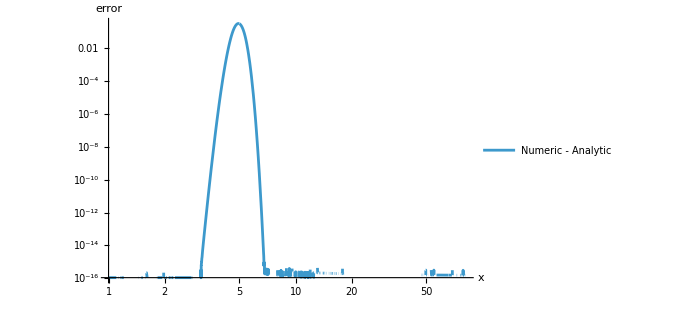

```mathematica
LogLogPlot[Abs[(Re@solNumericCont3[x]-(Re@solAnalyticExtended[γ[x]]))/(Re@solAnalyticExtended[γ[x]])],{x,1,100},PlotLegends->{"Numeric - Analytic"},AxesLabel->{"x","error"},PlotRange->All,ImageSize->500]
```

### Compare integration of Dirac delta function to the extended analytical solution with the extended Heaviside (Impose HLog boundary conditions)

```mathematica
SourceDelta=D[HeavisideTheta[r-r0]/.r0->5,r]
```

DiracDelta[-5+r]

```mathematica
ExtendedDiracDelta[r_,r0_]:=ⅈ/(π (r-r0))
```

```mathematica
HLog[r_,r0_]:=1+ I/Pi Log[r-r0]
```

```mathematica
Source=D[HLog[r,5],r]
```

ⅈ/(π (-5+r))

```mathematica
Plot[{Re[Source]/.r->a,Im[Source]/.r->a},{a,0,10}]
```

-Graphics-

```mathematica
Plot[{Re[Source]/.r->γ[a],Im[Source]/.r->γ[a]},{a,0,10}]
```

-Graphics-

```mathematica
ODE=Function[{r,l,S},D[ψ[r],{r,2}]+2/r D[ψ[r],{r,1}]-l(l+1)/r^2 ψ[r]==S]
```

Function[{r,l,S},∂_{r,2} ψ[r]+(2 ∂_{r,1} ψ[r])/r-(l (l+1) ψ[r])/r^2==S]

```mathematica
ODEHomo=ODE[r,0,SourceDelta]
```

(2 ψ'[r])/r+ψ''[r]==DiracDelta[-5+r]

```mathematica
solAnalyticExtended'[1]//N
```

0.+12.6233 ⅈ

```mathematica
HLog[1,5]
```

1+(ⅈ (ⅈ π+Log[4]))/π

```mathematica
BoundaryConditions={HLog[1,5],D[HLog[r,5],r]/.r->1}
```

{1+(ⅈ (ⅈ π+Log[4]))/π,-ⅈ/(4 π)}

```mathematica
(*Numerical solution (no Method specified)*)
solNumeric=NDSolveValue[{ODEHomo,ψ[1]==BoundaryConditions[[1]],ψ'[1]==BoundaryConditions[[2]]},ψ,{r,1,100},WorkingPrecision->50]
```

InterpolatingFunction[{{1.0000000000000000000000000000000000000000000000000, 100.00000000000000000000000000000000000000000000000}}, <>]

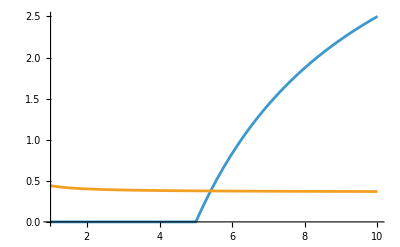

```mathematica
Plot[{Re@solNumeric[r],Im@solNumeric[r]},{r,1,10}]
```

```mathematica
solAnalytic=DSolveValue[{ODE[r,0,SourceDelta],ψ[1]==BoundaryConditions[[1]],ψ'[1]==BoundaryConditions[[2]]},ψ,r]//Simplify
```

Function[{r},(ⅈ-ⅈ r-100 π HeavisideTheta[-5+r]+20 π r HeavisideTheta[-5+r]+4 ⅈ r Log[4])/(4 π r)]

```mathematica
solAnalyticExtended=solAnalytic/.HeavisideTheta[-5+r]->HLog[r,5]
```

Function[{r},(ⅈ-ⅈ r-100 π (1+(ⅈ Log[-5+r])/π)+20 π r (1+(ⅈ Log[-5+r])/π)+4 ⅈ r Log[4])/(4 π r)]

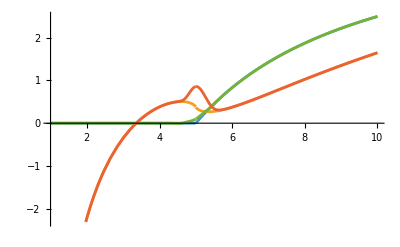

```mathematica
Plot[{Re@solAnalyticExtended[r],Im@solAnalyticExtended[r],Re@solAnalyticExtended[γ[r]],Im@solAnalyticExtended[γ[r]]},{r,1,10}]
```

```mathematica
ContourODEHomo3=Function[{a,l},Y''[a]+(-γpp[a]/γp[a]+2γp[a]/γ[a]) Y'[a]-l(l+1)γp[a]^2/γ[a]^2Y[a]==γp[a]^2 * (Source/.r->γ[a])]
```

Function[{a,l},Y''[a]+(-γpp[a]/γp[a]+(2 γp[a])/γ[a]) Y'[a]-(l (l+1) γp[a]^2 Y[a])/γ[a]^2==γp[a]^2 (Source/.r→γ[a])]

```mathematica
ContourODEHomo03=ContourODEHomo3[a,0]
```

((2 (1-20 ⅈ (-5+a) ⅇ^(-10 (-5+a)^2)))/(a+ⅈ ⅇ^(-10 (-5+a)^2))-(ⅈ (-20 ⅇ^(-10 (-5+a)^2)+400 (-5+a)^2 ⅇ^(-10 (-5+a)^2)))/(1-20 ⅈ (-5+a) ⅇ^(-10 (-5+a)^2))) Y'[a]+Y''[a]==(ⅈ (1-20 ⅈ (-5+a) ⅇ^(-10 (-5+a)^2))^2)/((-5+a+ⅈ ⅇ^(-10 (-5+a)^2)) π)

```mathematica
(* solAnalyticCont=DSolveValue[{ContourODEHomo[a,0],Y[1]==BoundaryConditions[[1]],Y'[1]==BoundaryConditions[[2]]},Y,a] *)
```

```mathematica
(*Solve along the contour:Y(a)=ψ(γ(a)) numerically *)
solNumericCont3=NDSolveValue[{ContourODEHomo3[a,0],Y[1]==BoundaryConditions[[1]],Y'[1]==BoundaryConditions[[2]]},Y,{a,1,100},WorkingPrecision->50]
```

InterpolatingFunction[{{1.0000000000000000000000000000000000000000000000000, 100.00000000000000000000000000000000000000000000000}}, <>]

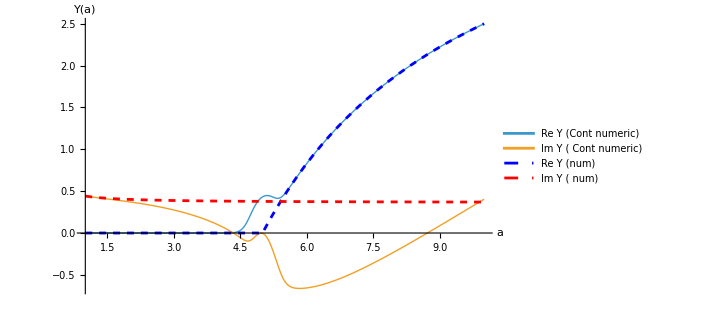

```mathematica
Plot[{Re[solNumericCont3[a]],Im[solNumericCont3[a]],Re[solNumeric[a]],Im[solNumeric[a]]},{a,1,10},PlotLegends->{"Re Y (Cont numeric)","Im Y ( Cont numeric)","Re Y (num)","Im Y ( num)"},AxesLabel->{"a","Y(a)"},PlotRange->All,ImageSize->520,PlotStyle->{{Thick},{Thick},{Dashed,Blue},{Dashed,Red}   }]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

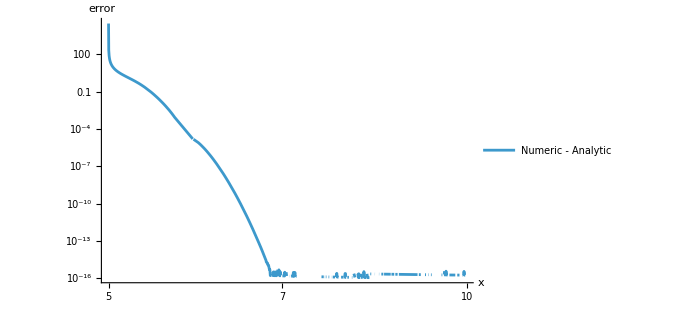

```mathematica
LogLogPlot[Abs[(Re@solNumericCont3[x]-(Re@solNumeric[x]))/(Re@solNumeric[x])],{x,1,10},PlotLegends->{"Numeric - Analytic"},AxesLabel->{"x","error"},PlotRange->All,ImageSize->500]
```

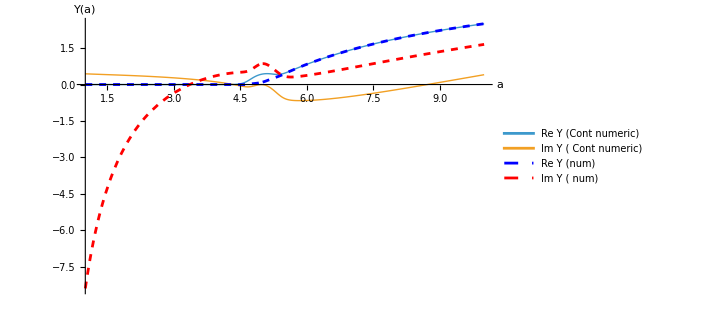

```mathematica
Plot[{Re[solNumericCont3[a]],Im[solNumericCont3[a]],Re@solAnalyticExtended[γ[a]],Im@solAnalyticExtended[γ[a]]},{a,1,10},PlotLegends->{"Re Y (Cont numeric)","Im Y ( Cont numeric)","Re Y (num)","Im Y ( num)"},AxesLabel->{"a","Y(a)"},PlotRange->All,ImageSize->520,PlotStyle->{{Thick},{Thick},{Dashed,Blue},{Dashed,Red}   }]
```

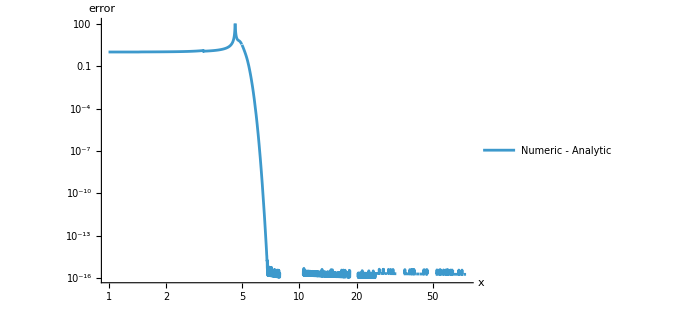

```mathematica
LogLogPlot[Abs[(Re@solNumericCont3[x]-(Re@solAnalyticExtended[γ[x]]))/(Re@solAnalyticExtended[γ[x]])],{x,1,100},PlotLegends->{"Numeric - Analytic"},AxesLabel->{"x","error"},PlotRange->All,ImageSize->500]
```